```mathematica
TrueVoltage = 3.0
```

3.

```mathematica
NoiseLevel=0.2
```

0.2

```mathematica
NoisyVoltage:=RandomVariate[NormalDistribution[TrueVoltage , NoiseLevel]]
```

A is the state transition matrix. Multiply the previous state by A to obtain the new state.

```mathematica
A={{1}}
```

{{1}}

B is the control matrix. Multiply any control factors by B; in this case, there are no control factors, so we could have let B be anything.

```mathematica
B={{0}}
```

{{0}}

H is the observation matrix. Multiply an incoming observation by H to obtain a state. In this case, we don’t modify the observations beforehand.

```mathematica
H={{1}}
```

{{1}}

Q is the process covariance; very small in this case.

```mathematica
Q={{0.0001}}
```

{{0.0001}}

R is the measurement covariance; also very small.

```mathematica
R={{0.1}}
```

{{0.1}}

X0 is the initial prediction for the state; we will set it to a vastly incorrect value.

```mathematica
X0={{7}}
```

{{7}}

P0 is the initial prediction for the covariance.

```mathematica
P0={{1}}
```

{{1}}

```mathematica
KalmanStep[A_,B_,H_,Q_,R_,{X_,P_},NewMeasurement_,NewControl_]:=(
(* Prediction step. *)
predictedStateEstimate=A.X + B.NewControl;
predictedProbEstimate = (A.P).Transpose[A]+Q;
(* Observation step. *)
innovation = NewMeasurement-H.predictedStateEstimate;
innovationCovariance = (H.predictedProbEstimate).Transpose[H]+R;
(* Update step. *)
kalmanGain = (predictedProbEstimate.Transpose[H]).Inverse[innovationCovariance];
newStateEstimate=predictedStateEstimate+kalmanGain.innovation;
size=First[Dimensions[P]];
newProbEstimate=(IdentityMatrix[size]-kalmanGain.H).predictedProbEstimate;
{newStateEstimate,newProbEstimate}
)
```

```mathematica
KalmanVoltageMapping[OldStateProb_,NewMeasurement_]:=KalmanStep[A,B,H,Q,R,OldStateProb,{{NewMeasurement}},{{0}}]
```

```mathematica
NumSamples=100
```

100

```mathematica
NoisySamples=Map[(NoisyVoltage)&,Range[NumSamples]]
```

{2.97138,2.9348,2.89892,3.00227,2.82656,2.79157,3.05589,2.80432,2.76732,3.06264,3.37769,3.19362,3.29521,2.6983,2.96283,3.08309,2.79644,3.06967,2.96943,2.91756,3.07103,2.99037,3.16422,2.93584,3.02501,3.62884,3.29186,2.84048,2.78929,3.15441,2.86381,2.95522,3.10668,2.66406,2.93885,3.14396,3.10688,3.0792,2.8875,3.07985,2.94046,3.16123,2.98041,3.04671,3.02062,2.7064,3.03495,3.01755,3.2779,3.20173,2.96094,3.00257,2.94175,2.81799,3.14207,2.99261,2.70593,3.17623,2.81163,2.9774,3.07112,3.14733,2.55964,2.8378,2.76494,3.32369,3.1145,3.09508,2.95447,2.95301,3.02899,3.23248,2.98257,3.11308,2.80842,3.07625,3.0079,2.72765,3.07476,2.95174,3.23142,3.1602,3.07328,2.92981,3.15614,3.15721,3.06437,2.71287,2.96872,2.94072,2.78843,2.92955,3.02668,2.98981,3.09611,3.07948,2.97868,3.00293,3.28201,3.21973}

```mathematica
KalmanData=FoldList[KalmanVoltageMapping,{X0,P0},NoisySamples]
```

{{{{7}},{{1}}},{{{3.33758}},{{0.0909099}}},{{{3.14567}},{{0.0476467}}},{{{3.06593}},{{0.0323166}}},{{{3.05034}},{{0.0244808}}},{{{3.00619}},{{0.0197308}}},{{{2.97067}},{{0.016549}}},{{{2.98284}},{{0.0142727}}},{{{2.9604}},{{0.0125666}}},{{{2.9387}},{{0.0112425}}},{{{2.95132}},{{0.0101871}}},{{{2.99109}},{{0.00932753}}},{{{3.00854}},{{0.00861532}}},{{{3.03152}},{{0.00801664}}},{{{3.00651}},{{0.0075073}}},{{{3.00342}},{{0.0070695}}},{{{3.00875}},{{0.00668987}}},{{{2.99525}},{{0.00635816}}},{{{2.99976}},{{0.00606638}}},{{{2.998}},{{0.00580823}}},{{{2.99352}},{{0.00557863}}},{{{2.99768}},{{0.00537349}}},{{{2.9973}},{{0.00518944}}},{{{3.00569}},{{0.00502372}}},{{{3.00228}},{{0.00487399}}},{{{3.00336}},{{0.00473831}}},{{{3.03223}},{{0.00461502}}},{{{3.04392}},{{0.00450271}}},{{{3.03496}},{{0.00440019}}},{{{3.02438}},{{0.00430639}}},{{{3.02987}},{{0.00422042}}},{{{3.023}},{{0.00414149}}},{{{3.02024}},{{0.00406891}}},{{{3.0237}},{{0.00400207}}},{{{3.00953}},{{0.00394043}}},{{{3.00678}},{{0.00388352}}},{{{3.01204}},{{0.00383091}}},{{{3.01562}},{{0.00378224}}},{{{3.018}},{{0.00373715}}},{{{3.01318}},{{0.00369535}}},{{{3.01562}},{{0.00365657}}},{{{3.01289}},{{0.00362057}}},{{{3.01821}},{{0.0035871}}},{{{3.01687}},{{0.00355599}}},{{{3.01792}},{{0.00352704}}},{{{3.01802}},{{0.00350009}}},{{{3.00719}},{{0.00347499}}},{{{3.00815}},{{0.0034516}}},{{{3.00847}},{{0.00342978}}},{{{3.01766}},{{0.00340944}}},{{{3.0239}},{{0.00339045}}},{{{3.02177}},{{0.00337273}}},{{{3.02113}},{{0.00335618}}},{{{3.01848}},{{0.00334072}}},{{{3.01181}},{{0.00332627}}},{{{3.01612}},{{0.00331277}}},{{{3.01535}},{{0.00330014}}},{{{3.00517}},{{0.00328833}}},{{{3.01078}},{{0.00327729}}},{{{3.00427}},{{0.00326695}}},{{{3.0034}},{{0.00325728}}},{{{3.0056}},{{0.00324823}}},{{{3.01019}},{{0.00323975}}},{{{2.99563}},{{0.00323182}}},{{{2.99054}},{{0.00322439}}},{{{2.98328}},{{0.00321743}}},{{{2.99421}},{{0.00321091}}},{{{2.99807}},{{0.0032048}}},{{{3.00117}},{{0.00319908}}},{{{2.99968}},{{0.00319371}}},{{{2.99819}},{{0.00318869}}},{{{2.99917}},{{0.00318398}}},{{{3.00659}},{{0.00317956}}},{{{3.00583}},{{0.00317542}}},{{{3.00923}},{{0.00317154}}},{{{3.00287}},{{0.0031679}}},{{{3.00519}},{{0.00316449}}},{{{3.00527}},{{0.00316129}}},{{{2.99651}},{{0.00315829}}},{{{2.99897}},{{0.00315547}}},{{{2.99749}},{{0.00315283}}},{{{3.00486}},{{0.00315036}}},{{{3.00975}},{{0.00314804}}},{{{3.01174}},{{0.00314586}}},{{{3.00917}},{{0.00314381}}},{{{3.01379}},{{0.0031419}}},{{{3.01829}},{{0.0031401}}},{{{3.01974}},{{0.00313841}}},{{{3.01011}},{{0.00313683}}},{{{3.00881}},{{0.00313534}}},{{{3.00668}},{{0.00313395}}},{{{2.99984}},{{0.00313264}}},{{{2.99764}},{{0.00313141}}},{{{2.99855}},{{0.00313026}}},{{{2.99828}},{{0.00312918}}},{{{3.00134}},{{0.00312817}}},{{{3.00378}},{{0.00312721}}},{{{3.003}},{{0.00312632}}},{{{3.00299}},{{0.00312548}}},{{{3.01171}},{{0.0031247}}},{{{3.01821}},{{0.00312396}}}}

```mathematica
KalmanSamples=Map[(Extract[First[#],{1,1}])&,KalmanData]
```

{7,3.33758,3.14567,3.06593,3.05034,3.00619,2.97067,2.98284,2.9604,2.9387,2.95132,2.99109,3.00854,3.03152,3.00651,3.00342,3.00875,2.99525,2.99976,2.998,2.99352,2.99768,2.9973,3.00569,3.00228,3.00336,3.03223,3.04392,3.03496,3.02438,3.02987,3.023,3.02024,3.0237,3.00953,3.00678,3.01204,3.01562,3.018,3.01318,3.01562,3.01289,3.01821,3.01687,3.01792,3.01802,3.00719,3.00815,3.00847,3.01766,3.0239,3.02177,3.02113,3.01848,3.01181,3.01612,3.01535,3.00517,3.01078,3.00427,3.0034,3.0056,3.01019,2.99563,2.99054,2.98328,2.99421,2.99807,3.00117,2.99968,2.99819,2.99917,3.00659,3.00583,3.00923,3.00287,3.00519,3.00527,2.99651,2.99897,2.99749,3.00486,3.00975,3.01174,3.00917,3.01379,3.01829,3.01974,3.01011,3.00881,3.00668,2.99984,2.99764,2.99855,2.99828,3.00134,3.00378,3.003,3.00299,3.01171,3.01821}

```mathematica
TrueSamples=Map[(TrueVoltage)&,Range[NumSamples]]
```

{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.}

In the graph below, red is the noisy sampling, blue is the Kalman-filtered data, and green is the ideal (true) data. Note that the blue (Kalman) line starts way up high since we gave a bad initial prediction.

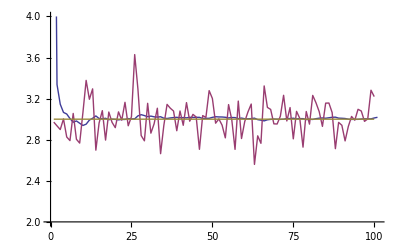

```mathematica
ListLinePlot[{KalmanSamples,NoisySamples,TrueSamples},PlotRange->{2,4}]
```